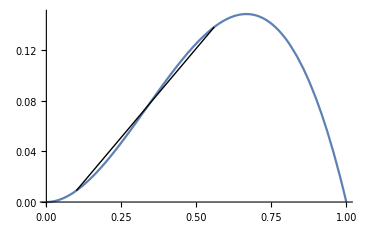

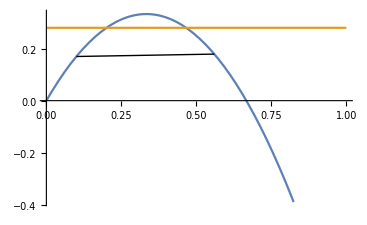

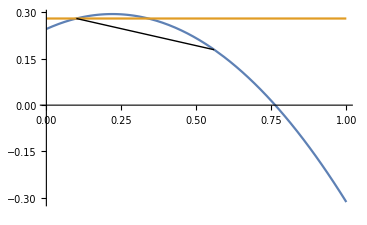

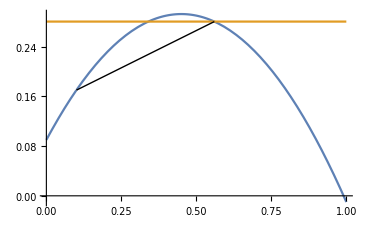

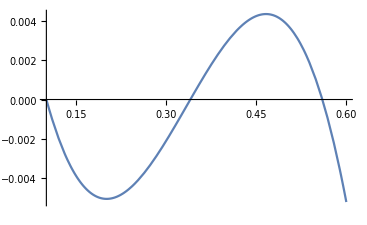

```mathematica
f[q_]:=(q^2-q^3)
qleft = 0.56;
qright = 0.1;
s[ql_,qr_]:= (f[ql]-f[qr])/(ql - qr);
Plot[f[q],{q,0,1},Epilog->{Line[{{qright,f[qright]},{qleft,f[qleft]}}]}]
Plot[{f'[q],s[qleft,qright]},{q,0,1},Epilog->{Line[{{qright,f'[qright]},{qleft,f'[qleft]}}]}]
Plot[{s[q,qleft],s[qleft,qright]},{q,0,1},Epilog->{Line[{{qright,s[qright,qleft]},{qleft,Limit[s[q,qleft],q->qleft]}}]}]
Plot[{s[q,qright],s[qleft,qright]},{q,0,1},Epilog->{Line[{{qright,Limit[s[q,qright],q->qright]},{qleft,s[qleft,qright]}}]}]
Plot[f[q]-(s[qleft,qright]*(q - qleft)+f[qleft]),{q,qright,0.6}]
```

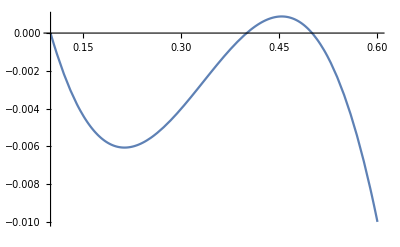

```mathematica
Plot[f[q]-(s[qleft,qright]*(q - qleft)+f[qleft]),{q,qright,0.6}]
```

```mathematica
Clear[s]
```

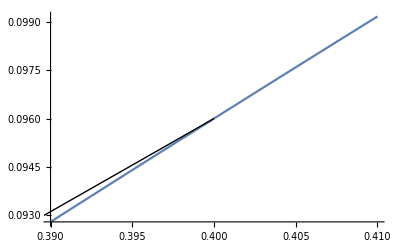

```mathematica
Plot[f[q],{q,.39,.41},Epilog->{Line[{{qright,f[qright]},{qleft,f[qleft]}}]}]
```

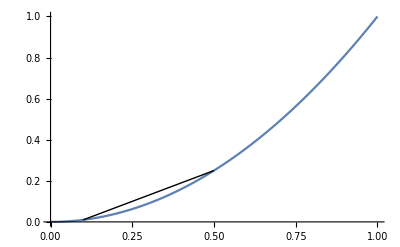

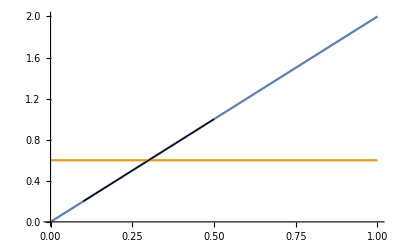

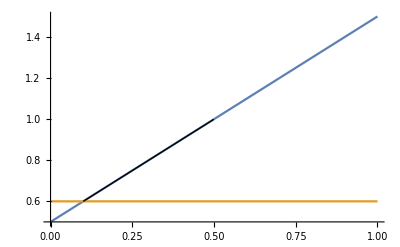

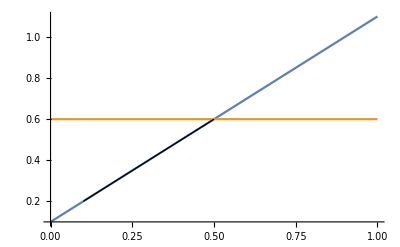

```mathematica
f[q_]:=(q^2)
qleft = 0.5;
qright = 0.1;
s[ql_,qr_]:= (f[ql]-f[qr])/(ql - qr);
Plot[f[q],{q,0,1},Epilog->{Line[{{qright,f[qright]},{qleft,f[qleft]}}]}]
Plot[{f'[q],s[qleft,qright]},{q,0,1},Epilog->{Line[{{qright,f'[qright]},{qleft,f'[qleft]}}]}]
Plot[{s[q,qleft],s[qleft,qright]},{q,0,1},Epilog->{Line[{{qright,s[qright,qleft]},{qleft,Limit[s[q,qleft],q->qleft]}}]}]
Plot[{s[q,qright],s[qleft,qright]},{q,0,1},Epilog->{Line[{{qright,Limit[s[q,qright],q->qright]},{qleft,s[qleft,qright]}}]}]
```

```mathematica
f[q_]:=(q^2-q^3)
qright = 0.1;
s[ql_,qr_]:= (f[ql]-f[qr])/(ql - qr);
Manipulate[Plot[f[q]-(s[qleft,qright]*(q - qleft)+f[qleft]),{q,qright,0.12}],{qleft,0.3,0.8}]
```